```mathematica
$Assumptions  = {α ∈ Reals, α>1, n ∈ Reals, n>0, Ib>0, Gmo>0, T1>0, T2> 0, M0>0, M0 ∈ Reals, T1 ∈Reals, T2 ∈ Reals, Element[y[t],Reals], Ω ∈ Reals, {Subscript[A, 0],Subscript[A, 1], Subscript[A, 2]} ∈ Reals χ1 ∈ Reals, χ2 ∈ Reals, κ ∈ Reals, K ∈ Reals, ω0 ∈ Reals, ForAll[k ,Element[Subscript[A,k],Reals]]}
Rz[θ_] := RotationMatrix[θ, {0,0,1}]
```

{α∈ℝ,α>1,n∈ℝ,n>0,Ib>0,Gmo>0,T1>0,T2>0,M0>0,M0∈ℝ,T1∈ℝ,T2∈ℝ,y[t]∈ℝ,Ω∈ℝ,{A_0,A_1,A_2}∈ℝ χ1∈ℝ,χ2∈ℝ,κ∈ℝ,K∈ℝ,ω0∈ℝ,∀_k A_k∈ℝ}

```mathematica
Id = -y + y^3 /(16 * 1.3^2) /. y-> A0 Cos[ω0 t] //TrigReduce
```

```mathematica
-1. A0 Cos[t ω0]+0.02773668639053254 A0^3 Cos[t ω0]+0.009245562130177513 A0^3 Cos[3 t ω0]
```

-1. A0 Cos[t ω0]+0.0277367 A0^3 Cos[t ω0]+0.00924556 A0^3 Cos[3 t ω0]

```mathematica
Derivatives and Effective Driving of EOMs
```

```mathematica
(*use 
y = a[t] e^(I Ω t) + hc;
  Subscript[A, k] = a^(k)[t] e^(I Ω t) + hc;
  Subscript[B, k] = i a^(k)[t] e^(I Ω t) + hc
*)


neglectDerivative = 3;
maxDerivative = 2 neglectDerivative -1;

neglectRules = {Subscript[A, k_/;k≥ neglectDerivative]->0, Subscript[B, k_/;k≥ neglectDerivative]->0};
derivativeRules =  {Subscript[A, k_] :> Subscript[A, k+1] +Ω Subscript[B, k],Subscript[B, k_] :> Subscript[B, k+1] - Ω Subscript[A, k]};
derivativeRulesBField =  {Subscript[A, k_] :> Subscript[A, k+1],Subscript[B, k_] :> Subscript[B, k+1]};

replaceIm =  {Subscript[A, k_] :> Subscript[B, k], Subscript[B, k_] :> -Subscript[A, k]}

(*Subscript[y, k] is the kth derivative of y *)
lhs = Table[Subscript[y, k], {k, 0, maxDerivative }];

Print["y^(k) expressed in terms of A_k, B_k"]
rhs = Table[0, {k, 0, maxDerivative }];
rhs[[1]] = Subscript[A, 0];
For[kk=2, kk≤ maxDerivative + 1, kk++,
rhs[[kk]] = rhs[[kk-1]];
rhs[[kk]] =rhs[[kk]] /. derivativeRules //Expand;
];
rhs //MatrixForm

Print["solve the of A_k, B_k in terms of the kth derivative of y"]
(*More variables than equations, have to set some derivatives a^(k)[t] *)
solsDerivative = Solve[Thread[lhs==rhs /.neglectRules], Join[{Table[Subscript[A, k], {k, 0,neglectDerivative-1}], Table[Subscript[B, k], {k, 0, neglectDerivative -1}]} ] //Flatten][[1]]

Print["lab-frame field up to an approximation"]
Bxlab = κ Sum[-1/Ω^(n+1) If[EvenQ[n],(-1)^(n/2)Subscript[B, n], (-1)^((n+1)/2)Subscript[A, n]], {n, 0,1}]
mxyFAC = I Ω Bxlab + (Bxlab /.derivativeRulesBField);
mxyFAC =  Re[mxyFAC]+(Im[mxyFAC ]/.replaceIm) //ComplexExpand 

(*ASSUME: spins in stationary state always. Calculate the rhs of the EOM *)
Print["RHS of EOM for VCO"]
rhsEOM = - K ω0 /2 (χ1 - I χ2) mxyFAC //Simplify//ExpandAll

(* for prefactors with i, get other A_k, B_k *)
rhsEOM = Re[rhsEOM]+(Im[rhsEOM ]/.replaceIm) //ComplexExpand

Collect[rhsEOM /. solsDerivative //Expand, y]

Collect[(rhsEOM /. solsDerivative )//.Subscript[y,k_]/;k≥2:>- Ω^2 Subscript[y,k-2] //Expand, y]
```

{A_k_:>B_k,B_k_:>-A_k}

y^(k) expressed in terms of A_k, B_k

(A_0
A_1+Ω B_0
-Ω^2 A_0+A_2+2 Ω B_1
-3 Ω^2 A_1+A_3-Ω^3 B_0+3 Ω B_2
Ω^4 A_0-6 Ω^2 A_2+A_4-4 Ω^3 B_1+4 Ω B_3
5 Ω^4 A_1-10 Ω^2 A_3+A_5+Ω^5 B_0-10 Ω^3 B_2+5 Ω B_4)

solve the of A_k, B_k in terms of the kth derivative of y

{A_0→y_0,A_1→-(7 Ω^4 y_1+10 Ω^2 y_3+3 y_5)/(8 Ω^4),A_2→-(Ω^4 y_0+2 Ω^2 y_2+y_4)/(4 Ω^2),B_0→-(-15 Ω^4 y_1-10 Ω^2 y_3-3 y_5)/(8 Ω^5),B_1→-(-5 Ω^4 y_0-6 Ω^2 y_2-y_4)/(8 Ω^3),B_2→-(Ω^4 y_1+2 Ω^2 y_3+y_5)/(4 Ω^3)}

lab-frame field up to an approximation

κ (A_1/Ω^2-B_0/Ω)

κ A_0+(κ A_2)/Ω^2

RHS of EOM for VCO

-1/2 K κ χ1 ω0 A_0+1/2 ⅈ K κ χ2 ω0 A_0-(K κ χ1 ω0 A_2)/(2 Ω^2)+(ⅈ K κ χ2 ω0 A_2)/(2 Ω^2)

-1/2 K κ χ1 ω0 A_0-(K κ χ1 ω0 A_2)/(2 Ω^2)+1/2 K κ χ2 ω0 B_0+(K κ χ2 ω0 B_2)/(2 Ω^2)

-3/8 K κ χ1 ω0 y_0+(13 K κ χ2 ω0 y_1)/(16 Ω)+(K κ χ1 ω0 y_2)/(4 Ω^2)+(3 K κ χ2 ω0 y_3)/(8 Ω^3)+(K κ χ1 ω0 y_4)/(8 Ω^4)+(K κ χ2 ω0 y_5)/(16 Ω^5)

-1/2 K κ χ1 ω0 y_0+(K κ χ2 ω0 y_1)/(2 Ω)

```mathematica
χ1Approx = T2^2 Δ/(1 + (Δ T2)^2)
χ1Approx /. {K-> 0.1, T2-> 1, reff -> 0.05 , Q-> 100, αod-> 1.25, Δ->0.2 } //N

T2^2 Δ/(1 + (Δ T2)^2 - T2^2 36)   /. {K-> 0.1, T2-> 1, reff -> 0.05 , Q-> 100, αod-> 1.25, Δ->0.2 } //N

dωχ =K Q reff /(2 αod)χ1Approx  /. {K-> 0.1, T2-> 1, reff -> 0.005 , Q-> 100, αod->1.25, Δ->0.2 } //N

Sqrt[1 - dωχ]
```

(T2^2 Δ)/(1+T2^2 Δ^2)

0.192308

-0.00572082

0.0384615

0.980581

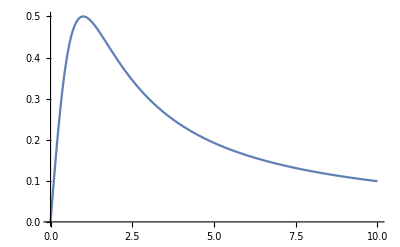

∀_k A_k∈ℝ

```mathematica
Plot[u /(1 + u^2), {u, 0, 10}]
```

```mathematica
YY[t_]:=a[t] Exp[I Ω t]
maxDerivative = 5;


eqs=Table[D[YY[t],{t,n}]//Expand,{n,0,maxDerivative}];

eqs  //MatrixForm

(*Ersetzung für a^(n)[t] e^(I Ω t)->A_n*)
replaceA={c_.Derivative[n_][a][t] Exp[I t Ω]/;FreeQ[c,a|t]:>c Subscript[A,n]};

(*Ersetzung für I Ω a^(n)[t] e^(I Ω t)->B_n*)
replaceB =  {Exp[I t Ω] -> 1, I -> 1}

rules={c_.*I*Exp[I t Ω]*Ω *a[t]:>c Subscript[B,0],
c_.*I*Exp[I t Ω]*Ω *Derivative[n_][a][t]:>c Subscript[B,n],
c_.*Exp[I t Ω]*Derivative[n_][a][t]:>c Subscript[A,n],
c_.*Exp[I t Ω]*a[t]:>c Subscript[A,0],
c_.I*Ω * Subscript[A,n]:>c Subscript[B,n]
};

rules2 = {
c_.flag *  Subscript[A,n_]:> c Subscript[B,n],
flag * c___:> c flag
};


test = ((eqs //. rules//ComplexExpand )/.Complex[0,2]-> 2 flag/Ω /. I -> flag / Ω) /. rules2//Simplify;
test //MatrixForm
Collect[test[[4]], flag]
```

(ⅇ^(ⅈ t Ω) a[t]
ⅈ ⅇ^(ⅈ t Ω) Ω a[t]+ⅇ^(ⅈ t Ω) a'[t]
-ⅇ^(ⅈ t Ω) Ω^2 a[t]+2 ⅈ ⅇ^(ⅈ t Ω) Ω a'[t]+ⅇ^(ⅈ t Ω) a''[t]
-ⅈ ⅇ^(ⅈ t Ω) Ω^3 a[t]-3 ⅇ^(ⅈ t Ω) Ω^2 a'[t]+3 ⅈ ⅇ^(ⅈ t Ω) Ω a''[t]+ⅇ^(ⅈ t Ω) a^(3)[t]
ⅇ^(ⅈ t Ω) Ω^4 a[t]-4 ⅈ ⅇ^(ⅈ t Ω) Ω^3 a'[t]-6 ⅇ^(ⅈ t Ω) Ω^2 a''[t]+4 ⅈ ⅇ^(ⅈ t Ω) Ω a^(3)[t]+ⅇ^(ⅈ t Ω) a^(4)[t]
ⅈ ⅇ^(ⅈ t Ω) Ω^5 a[t]+5 ⅇ^(ⅈ t Ω) Ω^4 a'[t]-10 ⅈ ⅇ^(ⅈ t Ω) Ω^3 a''[t]-10 ⅇ^(ⅈ t Ω) Ω^2 a^(3)[t]+5 ⅈ ⅇ^(ⅈ t Ω) Ω a^(4)[t]+ⅇ^(ⅈ t Ω) a^(5)[t])

{ⅇ^(ⅈ t Ω)→1,ⅈ→1}

(A_0
A_1+B_0
-Ω^2 A_0+A_2+2 B_1
-flag Ω^2 A_0-3 Ω^2 A_1+3 flag A_2+A_3
Ω^4 A_0-4 flag Ω^2 A_1-6 Ω^2 A_2+4 flag A_3+A_4
flag Ω^4 A_0+5 Ω^4 A_1-10 flag Ω^2 A_2-10 Ω^2 A_3+5 flag A_4+A_5)

-3 Ω^2 A_1+flag (-Ω^2 A_0+3 A_2)+A_3

```mathematica
test[[4]] //FullForm
```

Plus[Times[-1,flag,Power[\[CapitalOmega],2],Subscript[A,0]],Times[-3,Power[\[CapitalOmega],2],Subscript[A,1]],Times[3,flag,Subscript[A,2]],Subscript[A,3]]

```mathematica
Times[Complex[0,2]]
```

2 ⅈ

```mathematica
(*OLD *)
YY[t_]:=a[t] Exp[I Ω t]
maxDerivative = 5;


eqs=Table[D[YY[t],{t,n}]//Expand,{n,0,maxDerivative}]

rules=Table[Derivative[k][a][t] Exp[I Ω t]->Subscript[A, k],{k,0,maxDerivative}]

mat=eqs/.rules

ys=Table[Subscript[Y, k], {k, 0, maxDerivative}]

sol=Solve[Thread[ys==mat],Table[Subscript[A, k],{k,0,maxDerivative}]][[1]]

ClearAll[Asol, An,Bn, y]
(*An[n_] := Nest[D[#,t]-I Ω #&,y[t],n]//Expand*)

Un[n_]:=Nest[D[#,t]-I Ω #&,y[t],n]//Expand
UnStar[n_]:=Nest[D[#,t]+I Ω #&,y[t],n] //Expand;

An[n_] := (Un[n]+UnStar[n] )/2;
Bn[n_]:=I Ω (Un[n]-UnStar[n])/2

An[1]+Bn[0] //FullSimplify
Bn[0] 
An[1]
```

{ⅇ^(ⅈ t Ω) a[t],ⅈ ⅇ^(ⅈ t Ω) Ω a[t]+ⅇ^(ⅈ t Ω) a'[t],-ⅇ^(ⅈ t Ω) Ω^2 a[t]+2 ⅈ ⅇ^(ⅈ t Ω) Ω a'[t]+ⅇ^(ⅈ t Ω) a''[t],-ⅈ ⅇ^(ⅈ t Ω) Ω^3 a[t]-3 ⅇ^(ⅈ t Ω) Ω^2 a'[t]+3 ⅈ ⅇ^(ⅈ t Ω) Ω a''[t]+ⅇ^(ⅈ t Ω) a^(3)[t],ⅇ^(ⅈ t Ω) Ω^4 a[t]-4 ⅈ ⅇ^(ⅈ t Ω) Ω^3 a'[t]-6 ⅇ^(ⅈ t Ω) Ω^2 a''[t]+4 ⅈ ⅇ^(ⅈ t Ω) Ω a^(3)[t]+ⅇ^(ⅈ t Ω) a^(4)[t],ⅈ ⅇ^(ⅈ t Ω) Ω^5 a[t]+5 ⅇ^(ⅈ t Ω) Ω^4 a'[t]-10 ⅈ ⅇ^(ⅈ t Ω) Ω^3 a''[t]-10 ⅇ^(ⅈ t Ω) Ω^2 a^(3)[t]+5 ⅈ ⅇ^(ⅈ t Ω) Ω a^(4)[t]+ⅇ^(ⅈ t Ω) a^(5)[t]}

{ⅇ^(ⅈ t Ω) a[t]→A_0,ⅇ^(ⅈ t Ω) a'[t]→A_1,ⅇ^(ⅈ t Ω) a''[t]→A_2,ⅇ^(ⅈ t Ω) a^(3)[t]→A_3,ⅇ^(ⅈ t Ω) a^(4)[t]→A_4,ⅇ^(ⅈ t Ω) a^(5)[t]→A_5}

{A_0,ⅈ Ω A_0+A_1,-Ω^2 A_0+2 ⅈ Ω A_1+A_2,-ⅈ Ω^3 A_0-3 Ω^2 A_1+3 ⅈ Ω A_2+A_3,Ω^4 A_0-4 ⅈ Ω^3 A_1-6 Ω^2 A_2+4 ⅈ Ω A_3+A_4,ⅈ Ω^5 A_0+5 Ω^4 A_1-10 ⅈ Ω^3 A_2-10 Ω^2 A_3+5 ⅈ Ω A_4+A_5}

{Y_0,Y_1,Y_2,Y_3,Y_4,Y_5}

{A_0→Y_0,A_1→-ⅈ (Ω Y_0+ⅈ Y_1),A_2→-Ω^2 Y_0-2 ⅈ Ω Y_1+Y_2,A_3→ⅈ (Ω^3 Y_0+3 ⅈ Ω^2 Y_1-3 Ω Y_2-ⅈ Y_3),A_4→Ω^4 Y_0+4 ⅈ Ω^3 Y_1-6 Ω^2 Y_2-4 ⅈ Ω Y_3+Y_4,A_5→-ⅈ (Ω^5 Y_0+5 ⅈ Ω^4 Y_1-10 Ω^3 Y_2-10 ⅈ Ω^2 Y_3+5 Ω Y_4+ⅈ Y_5)}

y'[t]

0

y'[t]

```mathematica
ESR: Steady-State Bloch Equations in Rotating Frame
```

```mathematica
(*  eom of the form dot{M} = AA M + bb 
with ϵ = -γ B1, Δ = ωrot - ω0, B = (2 B1 cos(ωt), 0, B0), ω0 = -γ B0 < 0, ωrot = ω < 0 *)
AA = {{-1/T2, Δ, 0}, 
{-Δ, -1/T2, -ϵ},
{0, ϵ, -1/T1}};

bb = {0, 0, M0/T1};

(* for a spin system at temp. T, we have M0 = B0 χ0 with χ0 = N hbar.b2γ.b2/ 4 kB T *)
replacements = { ϵ ->  -γ B1, M0 -> NN hbar^2 γ^2 /( 4 kB T) };

Print["magnetization"]
M[Δ_, ϵ_, M0_, T1_, T2_]=-Inverse[AA].bb //FullSimplify 
M[Δ, -γ B1, M0, T1, T2]

Print["magnetization  in dimensionless units (see χ below)"]
MCalc[Δ_, B1_, M0_, T1_, T2_] = M[Δv γ B0 , -γ B1v B0, M0, T1v /(γ B0), T2v /(γ B0)] /. {Δv -> Δ, M0v-> M0, B1v-> B1, T1v-> T1, T2v-> T2} //FullSimplify;

Print["complex magnetization in steady state"]
MxyStSt[Δ_, ϵ_, M0_, T1_, T2_] = M[Δ, ϵ, M0, T1, T2][[1]]+ I M[Δ, ϵ, M0, T1, T2][[2]]
MxyStStCalc[Δ_, B1_, M0_, T1_, T2_] = MxyStSt[Δv γ B0 , -γ B1v B0, M0, T1v /(γ B0), T2v /(γ B0)] /. {Δv -> Δ, M0v-> M0, B1v-> B1, T1v-> T1, T2v-> T2} //FullSimplify;

Print["complex B-field in steady state"]
BxyStSt[ B1_] = B1 

Print["susceptibility in SI units "] 
χ[Δ_, M0_, B1_, T1_, T2_] = μ0 M[Δ, -γ B1, M0, T1, T2] / (B1) //FullSimplify

Print["susceptibility in dimensionless units "]
(* T1, T2 in units of 1/(γB0) 
  Δ in units of γB0
  B1 in units of B0
  M0 in units of B0/μ0
*)
χcalc[Δ_, M0_, B1_, T1_, T2_] =χ[Δv γ B0, M0v B0 /μ0, B1v B0, T1v /(γ B0), T2v /(γ B0)]/. {Δv -> Δ, M0v-> M0, B1v-> B1, T1v-> T1, T2v-> T2}//FullSimplify
```

magnetization

{-(M0 T2^2 Δ ϵ)/(1+T2^2 Δ^2+T1 T2 ϵ^2),-(M0 T2 ϵ)/(1+T2^2 Δ^2+T1 T2 ϵ^2),(M0+M0 T2^2 Δ^2)/(1+T2^2 Δ^2+T1 T2 ϵ^2)}

{(B1 M0 T2^2 γ Δ)/(1+B1^2 T1 T2 γ^2+T2^2 Δ^2),(B1 M0 T2 γ)/(1+B1^2 T1 T2 γ^2+T2^2 Δ^2),(M0+M0 T2^2 Δ^2)/(1+B1^2 T1 T2 γ^2+T2^2 Δ^2)}

magnetization  in dimensionless units (see χ below)

complex magnetization in steady state

-(ⅈ M0 T2 ϵ)/(1+T2^2 Δ^2+T1 T2 ϵ^2)-(M0 T2^2 Δ ϵ)/(1+T2^2 Δ^2+T1 T2 ϵ^2)

complex B-field in steady state

B1

susceptibility in SI units

{(M0 T2^2 γ Δ μ0)/(1+B1^2 T1 T2 γ^2+T2^2 Δ^2),(M0 T2 γ μ0)/(1+B1^2 T1 T2 γ^2+T2^2 Δ^2),((M0+M0 T2^2 Δ^2) μ0)/(B1+B1^3 T1 T2 γ^2+B1 T2^2 Δ^2)}

susceptibility in dimensionless units

{(M0 T2^2 Δ)/(1+B1^2 T1 T2+T2^2 Δ^2),(M0 T2)/(1+B1^2 T1 T2+T2^2 Δ^2),(M0+M0 T2^2 Δ^2)/(B1+B1^3 T1 T2+B1 T2^2 Δ^2)}

```mathematica
Spin Precession
```

```mathematica
(*  gives a Larmor frequency ωL = - γ B0
  choose ωL as a reference, and keep B0val = 1, such that ωL = -1 
*)
B0val = 1;

(* B1val = B1 / B0 *)
B1val = 0.1;

(* Δ = ω - ωL = ω - (-γ B1), given in units of |ωL|
 => Δval = (ω-ωL)/|ωL|
 attention, both ω, ωL < 0 
    => Δ> 0 means that ω > -1 , so ω is less negative 
    => Δ< 0 means that ω < -1 , so ω is more negative 
 *)
Δval = 0.0

(* frequency of the mw drive, should be negative *)
ωval = -1 + Δval;

(* all time units given in units of 1/|γB0|, so eg. T1 γB0 is dimensionless *)
T1val = 0.5;
T2val =0.5;
t0 = 0.0
tf = 16 π

(*initial magnetization in units of B0 / μ0 *)
M0val= {0,0,1};

(* give in units \vec{B}/B0 *)
Blab[t_, ω_, B1_] = {2B1 Cos[ω t], 0 B1 Sin[ω t], 1};


blochdgl = D[{Mx[t], My[t], Mz[t]}, {t,1}] - Cross[{Mx[t], My[t], Mz[t]},Blab[t, ωval,  B1val]] + {Mx[t]/T2, My[t]/T2, (Mz[t]-M0)/T1 }  /. {T1-> T1val, T2-> T2val, M0-> M0val[[3]]}

(* exact solution, time consuming *) 
(*
blochsol = DSolve[{blochdgl== {0, 0, 0} , Mx[0]==M0sol[[1]], My[0]==M0sol[[2]], Mz[0]==M0sol[[3]]}, {Mx, My, Mz}, t][[1]] /.Function[{t},body_]:>body

ClearAll[Msol]
Msol[t_] = {Mx, My, Mz}/.blochsol /. C[1]-> 1 /.C[2]-> 0  /. C[3]-> 1 /.Function[{t},body_]:>body

M0sol = Msol[0]
*)


(* numeric solution *)
blochsol = NDSolve[{blochdgl== {0, 0, 0}, Mx[0]==M0val[[1]], My[0]==M0val[[2]], Mz[0]==M0val[[3]]}, {Mx, My, Mz}, {t, t0, tf}][[1]]

Msol[t_] ={Mx[t],My[t],Mz[t]}/.blochsol ;

(* solution in rotating frame *)
Mxy[t_] = (Msol[t][[1]] + I Msol[t][[2]]) Exp[-I ωval t];
Bxy[t_] = (Blab[t,ωval, B1val][[1]] + I Blab[t,ωval, B1val][[2]]) Exp[-I ωval t];

(* complex susceptibility in rotating frame *)
χval = χcalc[Δval, M0val[[3]], T1val, T2val][[1]] + I χcalc[Δval, M0val[[3]], T1val, T2val][[2]]

(* Fourier solution and retarding χ in time space *)
χtime[t_, ωL_, T2_, M0_] = I M0 Exp[- t/T2] Exp[ I ωL t];

(* complex magnetization in lab frame *)
MxyConv[t_] =Integrate[χtime[t-τ, -1, T2val, M0val[[3]]] Blab[τ,ωval, B1val][[1]],{τ,0,t},Assumptions->t≥0]
```

0.

0.

16 π

{2. Mx[t]-My[t]+Mx'[t],Mx[t]+2. My[t]-0.2 Cos[1. t] Mz[t]+My'[t],0.2 Cos[1. t] My[t]+2. (-1+Mz[t])+Mz'[t]}

{Mx→InterpolatingFunction[…],My→InterpolatingFunction[…],Mz→InterpolatingFunction[…]}

0.+1. ⅈ

ⅇ^((-2.-1. ⅈ) t) ((-0.025-0.075 ⅈ)+(0.+0.05 ⅈ) ⅇ^(2. t)+(0.025+0.025 ⅈ) ⅇ^((2.+2. ⅈ) t))

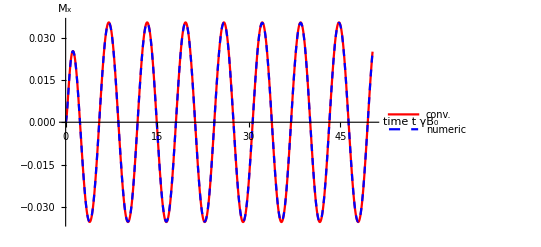

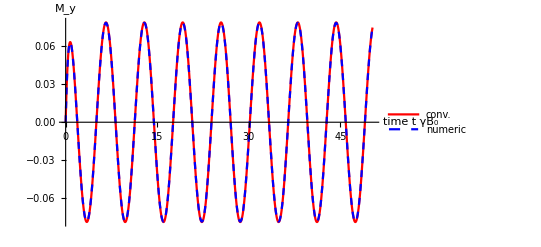

```mathematica
(* compare: numeric  solution to convolution with retarting χ(t)*)

STYLE = {{Red}, {Blue, Dashed}};
p1 = Plot[
{
MxyConv[t] //Re,
Msol[t][[1]]
}, {t, t0, tf}, AxesLabel->{"time t γB_0", "M_x"}, PlotLegends->Placed[{"conv.", "numeric"}, {0.8, 0.8}], PlotStyle->STYLE]

p2 = Plot[
{
MxyConv[t] //Im,
Msol[t][[2]]
}, {t, t0, tf}, AxesLabel->{"time t γB_0", "M_y"}, PlotLegends->Placed[{"conv.", "numeric"}, {0.8, 0.8}], PlotStyle->STYLE]
```

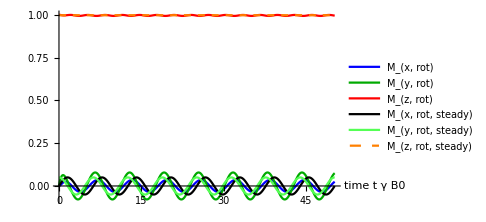

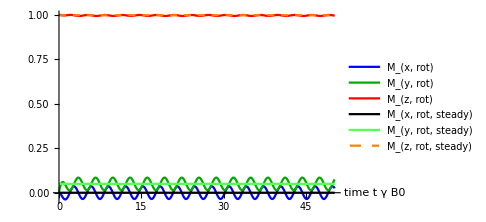

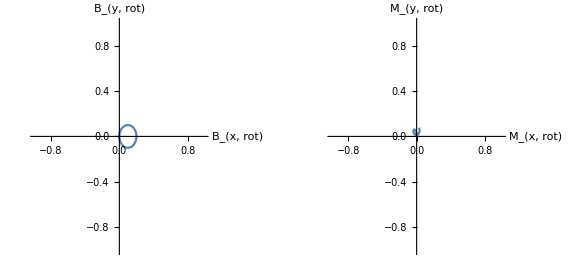

```mathematica
(*plot solutions in lab frame and in rotating frame *)
STYLE = {Blue, Darker[Green], Red, Black,Lighter[Green] , {Orange, Dashed}};

p1 = Plot[{
Msol[t][[1]],
Msol[t][[2]],
Msol[t][[3]],
MxyStStCalc[Δval, B1val, M0val[[3]], T1val, T2val]Exp[I ωval t] //Re,
MxyStStCalc[Δval, B1val, M0val[[3]], T1val, T2val]Exp[I ωval t] //Im,
MCalc[Δval, B1val, M0val[[3]], T1val, T2val][[3]]
}, {t, t0, tf}, 
AxesLabel->{"time t γ B0 "}, 
PlotLegends->Placed[{"M_(x, rot)", "M_(y, rot)", "M_(z, rot)", "M_(x, rot, steady)", "M_(y, rot,  steady)", "M_(z, rot, steady)"}, {0.8,0.6}], 
PlotStyle->STYLE,
ImageSize->Medium]
p2 = Plot[{
Mxy[t]  //Re,
Mxy[t] //Im,
Msol[t][[3]],
MCalc[Δval, B1val, M0val[[3]], T1val, T2val][[1]],
MCalc[Δval, B1val, M0val[[3]], T1val, T2val][[2]],
MCalc[Δval, B1val, M0val[[3]], T1val, T2val][[3]]
}, {t, t0, tf}, 
AxesLabel->{"time t γ B0 "},
 PlotLegends->Placed[{"M_(x, rot)", "M_(y, rot)", "M_(z, rot)", "M_(x, rot, steady)", "M_(y, rot,  steady)", "M_(z, rot, steady)"}, {0.8,0.6}], 
PlotStyle->STYLE,
 ImageSize->Medium]

par1 = ParametricPlot[{Re[Bxy[t]], Im[Bxy[t]]}, {t, t0, π}, PlotRange->{{-1,1},{-1,1}}, AxesLabel->{"B_(x, rot)", "B_(y, rot)"}];
par2 = ParametricPlot[{Re[Mxy[t]], Im[Mxy[t]]}, {t, t0, π}, PlotRange->{{-1,1},{-1,1}}, AxesLabel->{"M_(x, rot)", "M_(y, rot)"}];
GraphicsRow[{par1, par2}, ImageSize->Large]
```

```mathematica
FourierTransform[Cos[-Ω t] Exp[- t/T2] HeavisideTheta[t], t,ω,  FourierParameters->{-1, 1}, Assumptions-> {Ω ∈ Reals, T2> 0} ] //Simplify
```

(ⅈ T2 (ⅈ+T2 ω))/(2 π (ⅈ+T2 (ω-Ω)) (ⅈ+T2 (ω+Ω)))

```mathematica
test[t_, ωL_]=InverseFourierTransform[1/(A - I ω), ω, t, FourierParameters->{-1, 1}, Assumptions-> A>0 ]

Plot[test[t, -1] //Re, {t, 0,5}]
```

2 ⅇ^(-A t) π HeavisideTheta[t]

-Graphics-

0.0000621634+0.049782 ⅈ

0.1

0.+1. ⅈ

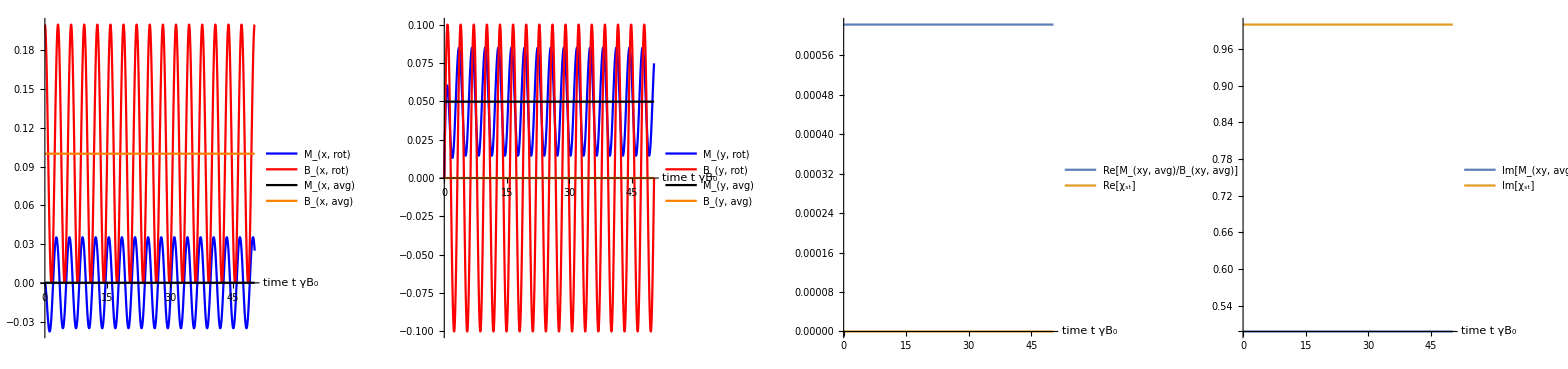

```mathematica
(*rotating frame: plot Magnetizations vs B-field *)

(* steady-state: averged magnetization, getting rid of fast oscillations due to non-RWA effects *)
MxyAVG= NIntegrate[Mxy[t], {t, 8π, 10π }] /(2π)
BxyAVG = NIntegrate[Bxy[t], {t,8π, 10π }] /(2π)
χval

p1 = Plot[{
Re[Mxy[t] ],
Re[Bxy[t] ], 
MxyAVG //Re,
BxyAVG //Re
}, {t, 0, tf}, AxesLabel->{"time t γB_0"}, PlotLegends->Placed[{"M_(x, rot)", "B_(x, rot)",  "M_(x, avg)", "B_(x, avg)"}, {0.8, 0.8}], PlotStyle->{Blue,Red, Black, Orange}];

p2 = Plot[{
Im[Mxy[t]],
Im[Bxy[t]],
MxyAVG //Im,
BxyAVG //Im
}, {t, 0, tf}, AxesLabel->{"time t γB_0"}, PlotLegends->Placed[{"M_(y, rot)", "B_(y, rot)", "M_(y, avg)", "B_(y, avg)"},{0.8, 0.8}], PlotStyle->{Blue,Red, Black, Orange}];

p3 = Plot[{
MxyAVG/BxyAVG //Re,
Re[χval]
}, {t, 0, tf},AxesLabel->{"time t γB_0"}, PlotLegends->Placed[{"Re[M_(xy, avg)/B_(xy, avg)]", "Re[χ_st]"},{0.7, 0.8}]];

p4 = Plot[{
MxyAVG/BxyAVG //Im,
Im[χval]
}, {t, 0, tf},AxesLabel->{"time t γB_0"}, PlotLegends->Placed[{"Im[M_(xy, avg)/B_(xy, avg)]", "Im[χ_st]"},{0.7, 0.8}]];


GraphicsRow[{p1,p2,  p3, p4}, ImageSize->Full]
```

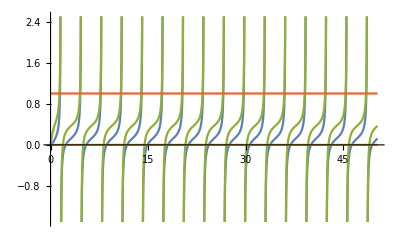

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

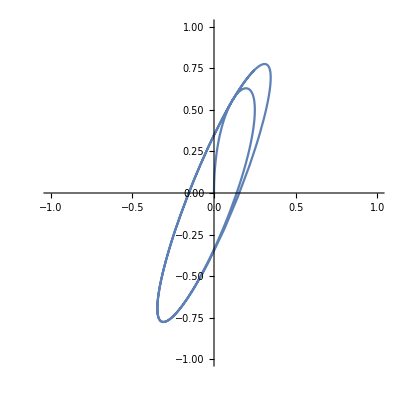

```mathematica
(* test plots for the susceptibility *)
Plot[{
Re[Mxy[t]/Bxy[t]],
Re[χval],
Im[Mxy[t]/Bxy[t]],
Im[χval]
}, {t, 0, tf}]

Plot[{
Re[(Msol[t][[1]] + I Msol[t][[2]])/(Blab[t,ωval, B0val, B1val][[1]] + I Blab[t,ωval, B0val, B1val][[2]] )],
Im[(Msol[t][[1]] + I Msol[t][[2]])/(Blab[t,ωval, B0val, B1val][[1]] + I Blab[t,ωval, B0val, B1val][[2]] )]
}, {t, 0, tf}]

ParametricPlot[{Re[Mxy[t] /(B1val Exp[-I ωval t])], Im[Mxy[t]/(B1val Exp[-I ωval t])]}, {t, t0,tf/4}, PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
Bloch Eqs in rotating frame
```

```mathematica
(* proof that (d/dt Rz) * Rz * Y = vec[w} x  Y *)
D[Inverse[Rz[ωrot τ]], {τ, 1}].Rz[ωrot τ] // TrigReduce

(* rot.-frame B field *) 
Brot = Inverse[Rz[ωrot t]].Blab[t, ω, B1]+ {0,0, ωrot}//TrigReduce

Brwa[t_ , B1_, Δ_] = Brot /. ωrot-> ω /. ω->  - 1 + Δ  /. Cos[_]-> 0/. Sin[_]-> 0//Simplify //TrigReduce


blochdglrwa = D[{Mx[t], My[t], Mz[t]}, {t,1}] - Cross[{Mx[t], My[t], Mz[t]}, Brwa[t, B1, Δ]] + {Mx[t]/T2, My[t]/T2, (Mz[t]-M0)/T1 } 

t0 = 0.0
tf = 16 π

M0val = {0.2,0,1}

rwasol = DSolve[{blochdglrwa== {0, 0, 0} , Mx[0]==M0val[[1]], My[0]==M0val[[2]], Mz[0]==M0val[[3]]}, {Mx, My, Mz}, t][[1]] /.Function[{t},body_]:>body;

Mrwa[t_, B1_, Δ_] ={Mx,My,Mz}/.rwasol ;

Mxyrwa[t_, B1_, Δ_] = Mrwa[t, B1, Δ][[1]] + I Mrwa[t, B1, Δ][[2]];
Bxyrwa[t_, B1_, Δ_] = Brwa[ t, B1, Δ][[1]] + I Brwa[t, B1, Δ][[2]];
```

{{0,ωrot,0},{-ωrot,0,0},{0,0,0}}

{B1 Cos[t ω-t ωrot]+B1 Cos[t ω+t ωrot],B1 Sin[t ω-t ωrot]-B1 Sin[t ω+t ωrot],1+ωrot}

{B1,0,Δ}

{Mx[t]/T2-Δ My[t]+Mx'[t],Δ Mx[t]+My[t]/T2-B1 Mz[t]+My'[t],B1 My[t]+(-M0+Mz[t])/T1+Mz'[t]}

0.

16 π

{0.2,0,1}

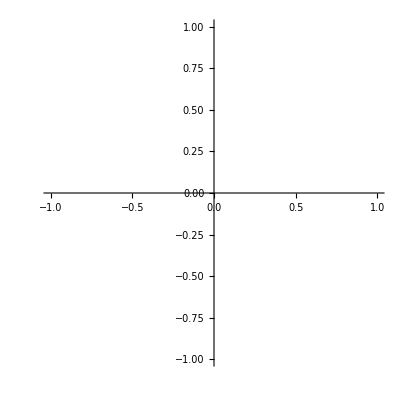

$Aborted

$Aborted

```mathematica
choosenumerical = {B1-> B1val, Δ-> 0, γ-> 1, T1-> 0.5, T2-> 0.5, M0 -> 1};

ParametricPlot[{Re[Bxyrwa[t, B1, Δ]], Im[Bxyrwa[t, B1, Δ]]} /. choosenumerical, {t, t0, π/2}, PlotRange->{{-1,1},{-1,1}}]
ParametricPlot[{Mrwa[t, B1, Δ], Mrwa[t, B1, Δ]} /. choosenumerical, {t, t0, tf}, PlotRange->{{-1,1},{-1,1}}]
Plot[{
Mrwa[t, B1, Δ][[1]]/. choosenumerical,
Mrwa[t,B1, Δ][[2]] /. choosenumerical,
Mrwa[t,B1, Δ][[3]]/.  choosenumerical
}, {t, t0, tf}]
```

```mathematica
Quiet[Manipulate[

Module[{r,curve,vec},

(*dgl solution *)
r[τ_?NumericQ]:=Rz[τ].Msol[τ];

curve=ParametricPlot3D[Evaluate[r[τ]],{τ,0,N[t]},PlotStyle->{Thick,Blue}];

vec=Graphics3D[{Red,Thick,Arrow[{{0,0,0},r[t]}]}];

Show[{
(*Sphere with radius of M0 *)
Graphics3D[{Opacity[0.1],Sphere[{0,0,0},Norm[r[0]]]}],
Graphics3D[{Opacity[0.1],Sphere[{0,0,0}, 1]}],
curve,
vec
},Axes->True,Boxed->True,PlotRange->1.2 Norm[r[0]] ,SphericalRegion->True, 
AxesLabel-> {"M_x/M_0", "M_y/M_0", "M_z/M_0"}
]


],{t,t0, tf, Animator}, Appearance -> Labeled, AnimationRate->(tf-t0)/10
],
{ParametricPlot3D::plld,NDSolve::precw}
]
```

ParametricPlot3D::plld: Endpoints for τ in {τ,0,N[FE`t$$452]} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot3D::plld will be suppressed during this calculation.

```mathematica
Linsted Method for VCOs
```

```mathematica
(* differential equation: it holds dgl = 0 *)
dgl = Ω D[x[t], {t,2}] +  x[t] +ϵ ((1-α) + 3α x[t]^2 /(8n^2)) D[x[t], {t,1}]

(* max. order of expansion for Linsted method *)
Nmaxorder = 2;
Ωrep = Ω -> ( 1 + Sum[ϵ^k * Subscript[ω, k], {k, 1, Nmaxorder}]);
xrep  =  x->(Sum[ϵ^k Subscript[x, k][#],{k,0,Nmaxorder}]&) //Expand;

(* list of dgl in orders of ϵ *)
dgllist = Table[SeriesCoefficient[dgl /. Ωrep /. xrep, {ϵ, 0, k}], {k, 0,
 Nmaxorder}]

(* list that stores solutions of orders of Ω *)
Ωsol = Table[Subscript[ω, k]-> Subscript[ω, k], {k, 1, Nmaxorder}];
```

x[t]+ϵ (1-α+(3 α x[t]^2)/(8 n^2)) x'[t]+Ω x''[t]

{x_0[t]+x_0''[t],x_1[t]+x_0'[t]-α x_0'[t]+(3 α x_0[t]^2 x_0'[t])/(8 n^2)+ω_1 x_0''[t]+x_1''[t],x_2[t]+(3 α x_0[t] x_1[t] x_0'[t])/(4 n^2)+x_1'[t]-α x_1'[t]+(3 α x_0[t]^2 x_1'[t])/(8 n^2)+ω_2 x_0''[t]+ω_1 x_1''[t]+x_2''[t]}

```mathematica
Print["0th order"]
dgllist[[1]]

Print["---solution "]
x0sol[t_] = A0 Cos[t]
Print[""]
```

0th order

x_0[t]+x_0''[t]

---solution

A0 Cos[t]

```mathematica
Print["1st order"]
eq =dgllist[[2]] /. Subscript[x, 0]-> (x0sol[#] &)  //TrigReduce 

Print["---coefficients that must be zero"]
coeffs=Coefficient[eq,{Cos[t],Sin[t]}] //Simplify

Print["--- new solutions for Ω and A"]
Ωsol[[1]] = Subscript[ω, 1]-> 0
Asol =  Solve[coeffs[[2]]==0, A0][[3]][[1]] //Simplify

Print["--- new eom"]
eq  ==0 /. Asol /. Ωsol //Simplify
ClearAll[sol]

Print["---solution "]
sol =Subscript[x, 1]/.DSolve[eq  ==0 /. Asol /. Ωsol//Simplify, Subscript[x, 1], t][[1,1]]
x1sol[t_] =(( sol/.Function[{t},body_]:>body)//TrigReduce) /. C[1]-> 0 /. C[2]->0 //Simplify
```

1st order

1/(64 n^2)(-64 A0 n^2 Sin[t]-3 A0^3 α Sin[t]+64 A0 n^2 α Sin[t]-3 A0^3 α Sin[3 t]-64 A0 n^2 Cos[t] ω_1+64 n^2 x_1[t]+64 n^2 x_1''[t])

---coefficients that must be zero

{-A0 ω_1,A0 (-1+α)-(3 A0^3 α)/(64 n^2)}

--- new solutions for Ω and A

ω_1→0

A0→(8 n √((-1+α)/α))/(√3)

--- new eom

(8 n (√((-1+α)/α)-√((-1+α) α)) Sin[3 t])/(√3)+x_1[t]+x_1''[t]==0

---solution

Function[{t},C[1] Cos[t]+C[2] Sin[t]+1/(√3)n (√((-1+α)/α)-√((-1+α) α)) (4 Cos[t]^2 Sin[t]+Cos[4 t] Sin[t]+2 Cos[t] Sin[2 t]-Cos[t] Sin[4 t])]

(n (√((-1+α)/α)-√((-1+α) α)) (2 Sin[t]+Sin[3 t]))/(√3)

```mathematica
Print["2nd order"]
eq =dgllist[[3]] /. Subscript[x, 0]-> (x0sol[#] &) /. Subscript[x, 1]-> (x1sol[#] &)  /. Asol /.Ωsol//TrigReduce

Print["coefficients that must be zero"]
coeffs=Coefficient[eq,{Cos[t],Sin[t]}] //Simplify

Ωsol[[2]]=Solve[coeffs[[1]]==0, Subscript[ω, 2]][[1,1]] //Simplify
```

2nd order

1/3 (-√3 n √((-1+α)/α) Cos[t]+√3 n √((-1+α)/α) α Cos[t]+√3 n √((-1+α) α) Cos[t]-√3 n α √((-1+α) α) Cos[t]-9 √3 n √((-1+α)/α) Cos[3 t]+9 √3 n √((-1+α)/α) α Cos[3 t]+9 √3 n √((-1+α) α) Cos[3 t]-9 √3 n α √((-1+α) α) Cos[3 t]-5 √3 n √((-1+α)/α) Cos[5 t]+5 √3 n √((-1+α)/α) α Cos[5 t]+5 √3 n √((-1+α) α) Cos[5 t]-5 √3 n α √((-1+α) α) Cos[5 t]-8 √3 n √((-1+α)/α) Cos[t] ω_2+3 x_2[t]+3 x_2''[t])

coefficients that must be zero

{-(n (√((-1+α)/α)-2 √((-1+α) α)+√((-1+α) α^3)+8 √((-1+α)/α) ω_2))/(√3),0}

ω_2→-1/8 (-1+α)^2

```mathematica
Atot = A0 /. Asol
Ωtot = (Ω /. Ωrep) /. Ωsol /. ϵ -> 1/Q
```

(8 n √((-1+α)/α))/(√3)

1-(-1+α)^2/(8 Q^2)

```mathematica
C
```

C

```mathematica
- 1/CC ( Gt - Gmo /2) /. Gmo -> 2 α Gt /. Gt -> CC ω0 / Q //Simplify
ϵ /CC * (x^2 / Ib^2) /. x->  Ib y /Gmo /. ϵ-> 3Gmo^3 /(16n^2)/. Gmo -> 2 α Gt /. Gt -> CC ω0 / Q 
- β x /(4 Sqrt[n]) Sqrt[4 Ib / β - x^2] /. β-> Gmo^2 n / Ib /. x->  Ib y /Gmo //Simplify
```

((-1+α) ω0)/Q

(3 y^2 α ω0)/(8 n^2 Q)

-1/4 Ib y √(4-n y^2)

```mathematica
Normal@Series[-1/4 Ib y √(4-n y^2), {y, 0, 4}] /. y-> Gmo x / Ib
```

-(Gmo x)/2+(Gmo^3 n x^3)/(16 Ib^2)

```mathematica
Series[1/(1 + ϵ ), {ϵ, 0, 2}]
```

1-ϵ+ϵ^2+O[ϵ]^3